# PolarGame

```mathematica
Quit
```

```mathematica
nb1=NotebookOpen[FileNameJoin[{NotebookDirectory[],"Common.nb"}]];
SelectionMove[nb1,All,Notebook]
SelectionEvaluate[nb1]
SetSelectedNotebook[EvaluationNotebook[]];
```

```mathematica
<<MaTeX`
SetDirectory[NotebookDirectory[]];
```

## Construction

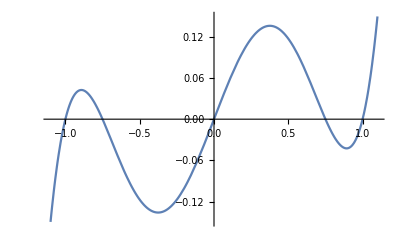

```mathematica
c1=1;
c2=0.75;
Plot[(-c1-x)*(-c2-x)*x*(-c1+x)*(-c2+x),{x,-1.1,1.1}]
```

```mathematica
Clear[a,b];
c1=1;
c2=3/4;
r'[t]=-a*(-c1-r[t])*(-c2-r[t])*r[t]*(-c2+r[t])*(-c1+r[t]);
theta'[t]=-b*r[t];
polar={r'[t],theta'[t]};-Evaluate@(TransformedField["Polar"->"Cartesian",polar,{r[t],theta[t]}->{x,y}]//FullSimplify)
```

{-b y+1/16 a x (-1+x^2+y^2) (-9+16 x^2+16 y^2),b x+1/16 a y (-1+x^2+y^2) (-9+16 x^2+16 y^2)}

```mathematica
W[x_,y_]:={-b y+1/16 a x (-1+x^2+y^2) (-9+16 x^2+16 y^2),b x+1/16 a y (-1+x^2+y^2) (-9+16 x^2+16 y^2)}
```

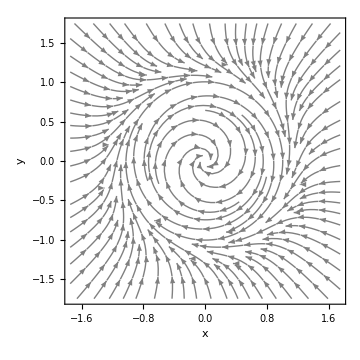

```mathematica
a=1;b=1;
plotFlow[W]
```

```mathematica
Clear[a,b];
$Assumptions=x∈Reals&&y∈Reals;
sides=11/10;
cons=-sides<=x<=sides&&-sides<=y<=sides;
star={0,0};
weakMVIcondition[x_,y_]:=Evaluate@(W[x,y]).({x,y}-star)/Norm[W[x,y]]^2;
J[x_,y_]:=Evaluate@(D[W[x,y],{{x,y}}]);
LocalLips[x_,y_]:=Norm[J[x,y],2];
```

```mathematica
a=1;b=1;
Show[
ContourPlot[weakMVIcondition[x,y],{x,-sides,sides},{y,-sides,sides},PlotLegends->Automatic,Contours->50,PlotLabel->"Local ρ"],plotMultipleTrajectories[W,{{1,1}},{{0,0.1}},25,50,7/4,True]]
```

-Graphics-

## ρ∈(-1/L,-1/2L)

```mathematica
a=1;b=1;
```

```mathematica
ρ=MinValue[{weakMVIcondition[x,y],cons},{x,y}]//Simplify
ArgMin[{weakMVIcondition[x,y],cons},{x,y}]//Simplify
N[ρ]
```

-50176/1050977

{0,-5/(4 √2)}

-0.0477422

```mathematica
L=MaxValue[{
LocalLips[x,y],cons},{x,y}]//Simplify
N[-1/(2L)]
```

(√(70246989617+2538096 √704424929))/20000

-0.0269572

```mathematica
ρ<-1/(2L)
ρ>-1/(1L)
```

True

True

## ρ∈(-1/2L,-1/3L)

```mathematica
a=3/4;b=1;
```

```mathematica
ρ=MinValue[{weakMVIcondition[x,y],cons},{x,y}]//Simplify
ArgMin[{weakMVIcondition[x,y],cons},{x,y}]//Simplify
N[ρ]
```

-602112/16798825

{0,-5/(4 √2)}

-0.0358425

```mathematica
L=Assuming[{x∈Reals,y∈Reals},MaxValue[{
LocalLips[x,y],cons},{x,y}]//Simplify]
N[-1/(2L)]
```

(√(635022906553+7614288 √6383574361))/80000

-0.0358721

```mathematica
ρ<-1/(3L)
ρ>-1/(2L)
```

True

True

## ρ∈(-1/8L,-1/10L)

```mathematica
a=1/3;b=1;
```

```mathematica
ρ=MinValue[{weakMVIcondition[x,y],cons},{x,y}]//Simplify
ArgMin[{weakMVIcondition[x,y],cons},{x,y}]//Simplify
N[ρ]
```

-150528/9439585

{0,-5/(4 √2)}

-0.0159465

```mathematica
L=Assuming[{x∈Reals,y∈Reals},MaxValue[{
LocalLips[x,y],cons},{x,y}]//Simplify]
N[-1/(8L)]
```

(√(73446989617+2538096 √754424929))/60000

-0.0198221

```mathematica
ρ>-1/(8L)
ρ<-1/(10L)
```

True

True

## Plotting

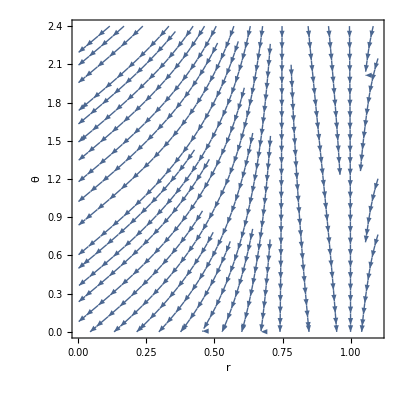

Figs/PolarGame_polar.png

```mathematica
a=1;b=1;
side=11/10;
StreamPlot[{r'[t],theta'[t]},{r[t],0,1.1},{theta[t],0,2.4},FrameLabel->{"r","θ"},StreamPoints->100]
Export["Figs/PolarGame_polar.png",%]
```

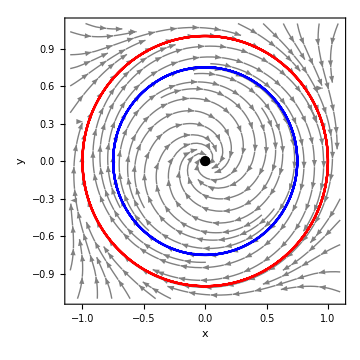

Figs/PolarGame_car.png

```mathematica
plot=plotMultipleTrajectories[W,{{1,1}},{{0.0,0.1}},25,50,side,True]
Export["Figs/PolarGame_car.png",%]
```